# Superimposed Kerr Metric in Kerr-Schild coordinates.

## Import metric

```mathematica
ClearAll[llgSKS,uugSKS];
Import["~/llgsks.mx"];
Import["~/uugsks.mx"];

llgSKS=(llgSKS//.Ω->Sqrt[(M1+M2)/b^3]);
uugSKS=(uugSKS//.Ω->Sqrt[(M1+M2)/b^3]);
```

## Plot definitions

```mathematica
ClearAll[M1,M2,a1,a2,b]
M1=1/2;
M2=1/2;
a1=98/100*M1;
a2=98/100*M2;
b=20;

Print[N[a1]];
```

0.49

## ADM components

```mathematica
ClearAll[ll4metric,uu4metric];
ll4metric=llgSKS;
uu4metric=uugSKS;

ClearAll[coords];
coords={t,x,y,z};

(*Spatial coordinates*)
ClearAll[spaceCoords];
spaceCoords=coords[[2;;4]];

ClearAll[llsmetric,uusmetric];
llsmetric=ll4metric[[2;;4,2;;4]];
uusmetric=Inverse[llsmetric];

ClearAll[lapse];
lapse=Sqrt[-1/uu4metric[[1,1]]];

ClearAll[lshift,ushift];
lshift=ll4metric[[1,2;;4]];
ushift=lapse^2*uu4metric[[1,2;;4]];

ClearAll[Γ,Dd];
Γ=Table[
Sum[1/2*uusmetric[[i,l]]*(D[llsmetric[[l,j]],spaceCoords[[k]]]+D[llsmetric[[l,k]],spaceCoords[[j]]]-D[llsmetric[[j,k]],spaceCoords[[l]]]),{l,1,3}],{i,1,3},{j,1,3},{k,1,3}
];

Dd[b_,c_,f_]:=D[f[[c]],spaceCoords[[b]]]-Sum[Γ[[d,b,c]] f[[d]],{d,1,3}];

ClearAll[llextrinsic,ulextrinsic];
llextrinsic=1/(2*lapse)*Table[-D[llsmetric[[i,j]],coords[[1]]]+Dd[i,j,lshift]+Dd[j,i,lshift],{i,1,3},{j,1,3}];
ulextrinsic=Table[Sum[uusmetric[[i,k]]*llextrinsic[[k,j]],{k,1,3}],{i,1,3},{j,1,3}];
```

## Plots

### Ergosphere

```mathematica
N[llgSKS⟦1,1⟧//.{t->0,x->b/2+10/10,y->0,z->0}]
```

0.340427

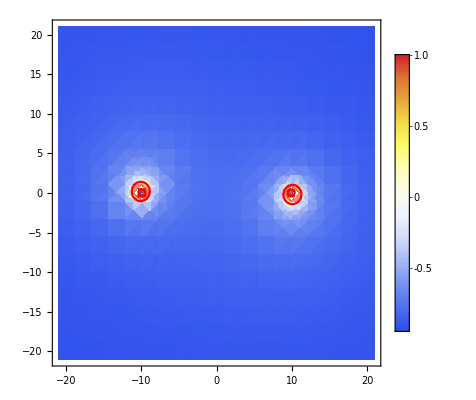

```mathematica
Block[
{Tval,ΩVal,expr},
ΩVal=Sqrt[(M1+M2)/b^3];
Tval=0/ΩVal;

expr=(llgSKS⟦1,1⟧)//.{t->Tval,z->0};

Show[
DensityPlot[
expr,
{x,-b-1,b+1},
{y,-b-1,b+1},

PlotPoints->20,
ColorFunction->"TemperatureMap",
PlotLegends->True,
PlotRange->{Full,Full,{-1,1}}
],

ContourPlot[
expr==0,
{x,-b-1,b+1},
{y,-b-1,b+1},

PlotPoints->20,
ContourShading->None,
ContourStyle->Directive[Red,Thick],
PlotLegends->False,
PlotRange->{Full,Full,{-1,1}}
]
]
]
```

### Determinant

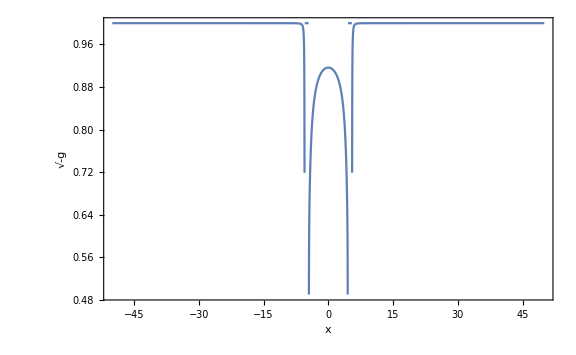

```mathematica
Block[
{expr},
expr=Sqrt[-Det[llgSKS]]//.{t->0,y->0,z->0};

Plot[expr,{x,-50,50},PlotRange->Full,FrameLabel->{"x","√-g"},Axes->False,Frame->True,ImageSize->Large]
]
```

### Lapse

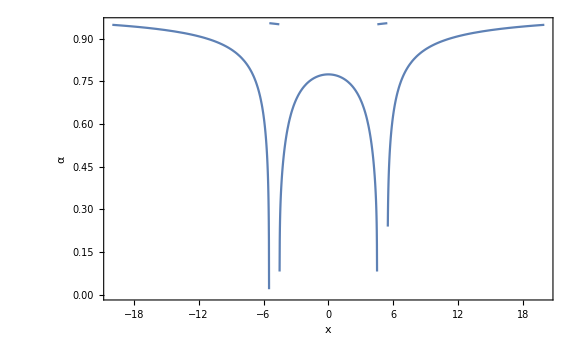

```mathematica
Block[
{expr},
expr=lapse//.{t->0,y->0,z->0};

Plot[expr,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","α"},Axes->False,Frame->True,ImageSize->Large]
]
```

### Lower Shift

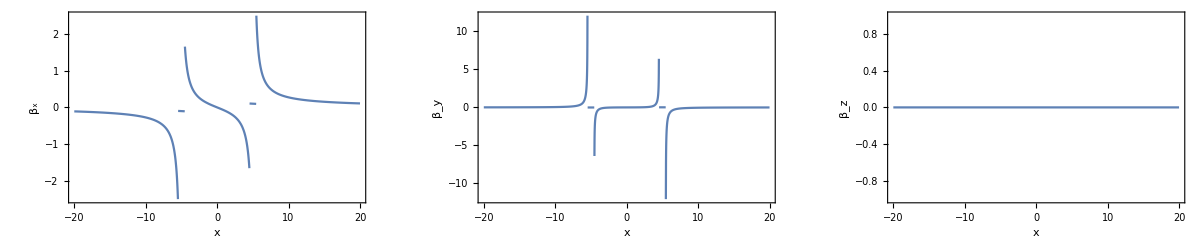

```mathematica
Block[
{expr1,expr2,expr3},

expr1=lshift⟦1⟧//.{t->0,y->0,z->0};
expr2=lshift⟦2⟧//.{t->0,y->0,z->0};
expr3=lshift⟦3⟧//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","β_x"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","β_y"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr3,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","β_z"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
]
```

### Upper Shift

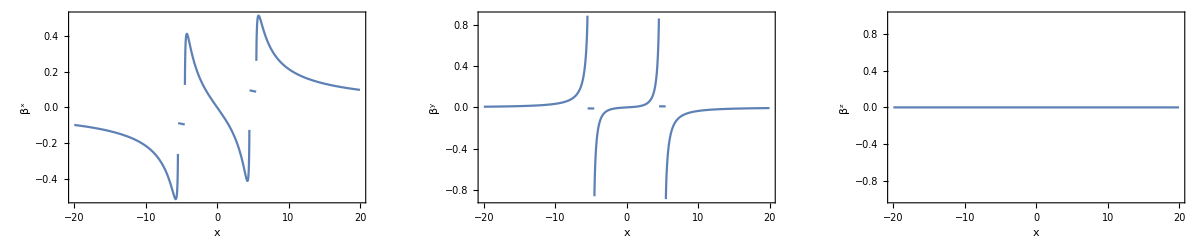

```mathematica
Block[
{expr1,expr2,expr3},

expr1=ushift⟦1⟧//.{t->0,y->0,z->0};
expr2=ushift⟦2⟧//.{t->0,y->0,z->0};
expr3=ushift⟦3⟧//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","β^x"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","β^y"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr3,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","β^z"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
]
```

### lower spatial metric

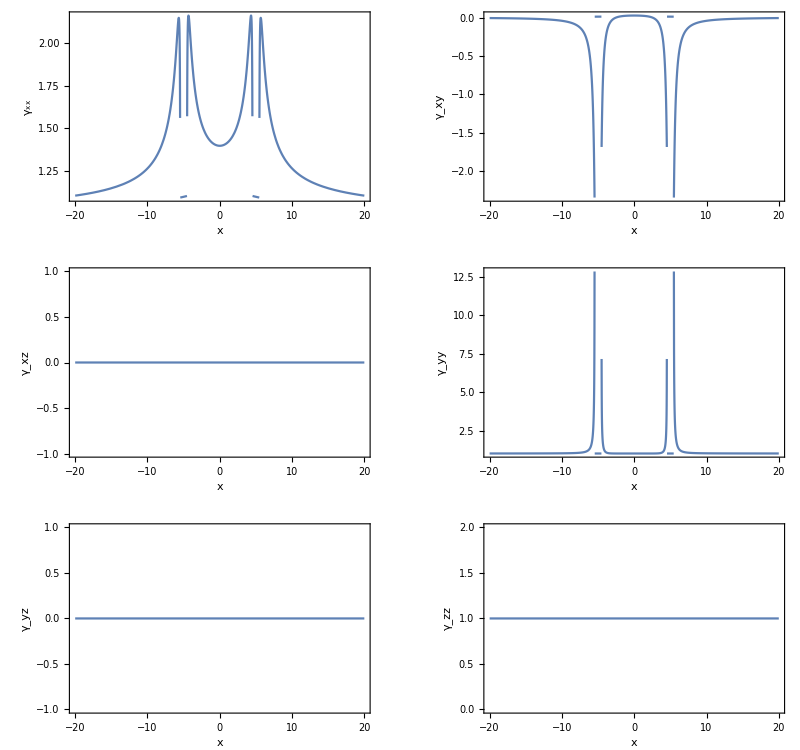

```mathematica
Block[
{expr1,expr2,expr3,expr4,expr5,expr6},

expr1=llsmetric⟦1,1⟧//.{t->0,y->0,z->0};
expr2=llsmetric⟦1,2⟧//.{t->0,y->0,z->0};
expr3=llsmetric⟦1,3⟧//.{t->0,y->0,z->0};
expr4=llsmetric⟦2,2⟧//.{t->0,y->0,z->0};
expr5=llsmetric⟦2,3⟧//.{t->0,y->0,z->0};
expr6=llsmetric⟦3,3⟧//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_xx"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_xy"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr3,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_xz"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr4,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_yy"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr5,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_yz"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr6,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_zz"},Axes->False,Frame->True,ImageSize->Large],
}
},
ImageSize->Full
]
]
```

### Upper spatial metric

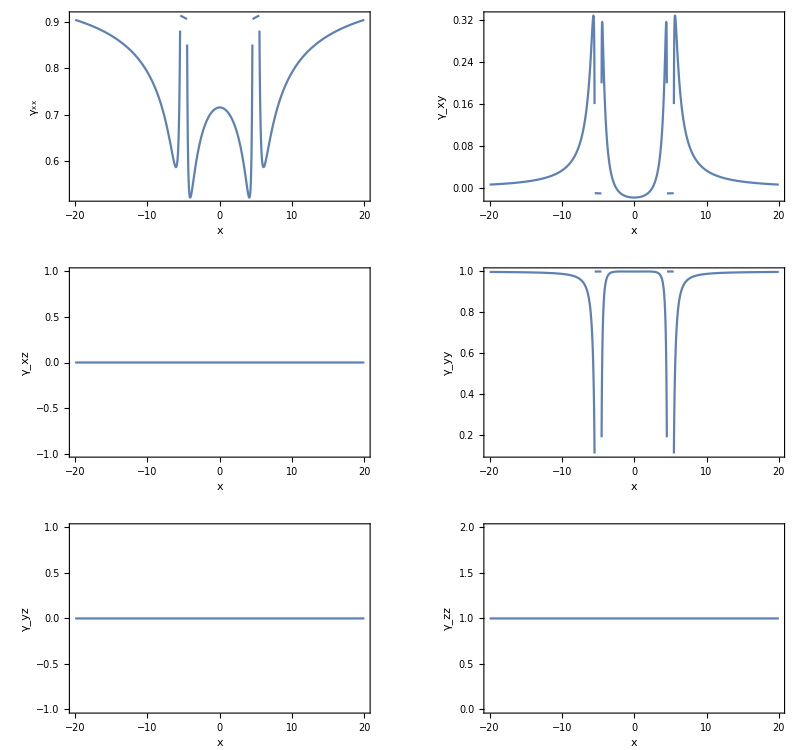

```mathematica
Block[
{expr1,expr2,expr3,expr4,expr5,expr6},

expr1=uusmetric⟦1,1⟧//.{t->0,y->0,z->0};
expr2=uusmetric⟦1,2⟧//.{t->0,y->0,z->0};
expr3=uusmetric⟦1,3⟧//.{t->0,y->0,z->0};
expr4=uusmetric⟦2,2⟧//.{t->0,y->0,z->0};
expr5=uusmetric⟦2,3⟧//.{t->0,y->0,z->0};
expr6=uusmetric⟦3,3⟧//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_xx"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_xy"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr3,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_xz"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr4,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_yy"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr5,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_yz"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr6,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","γ_zz"},Axes->False,Frame->True,ImageSize->Large],
}
},
ImageSize->Full
]
]
```

### Grad lapse

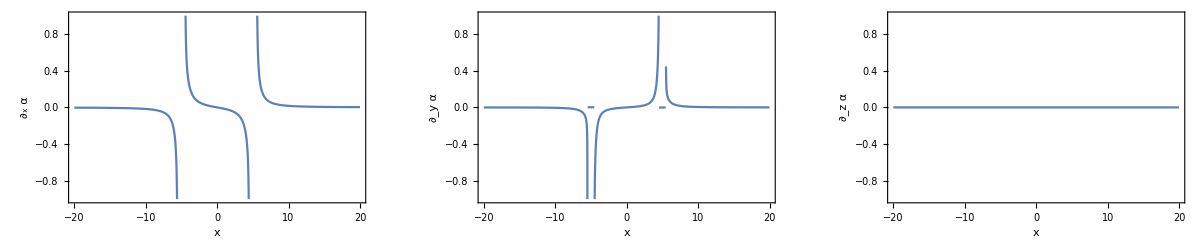

```mathematica
Block[
{expr1,expr2,expr3},

expr1=D[lapse,x]//.{t->0,y->0,z->0};
expr2=D[lapse,y]//.{t->0,y->0,z->0};
expr3=D[lapse,z]//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,{-1,1}},FrameLabel->{"x","∂_x α"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,{-1,1}},FrameLabel->{"x","∂_y α"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr3,{x,-20,20},PlotRange->{Full,{-1,1}},FrameLabel->{"x","∂_z α"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
]
```

### Grad ushift

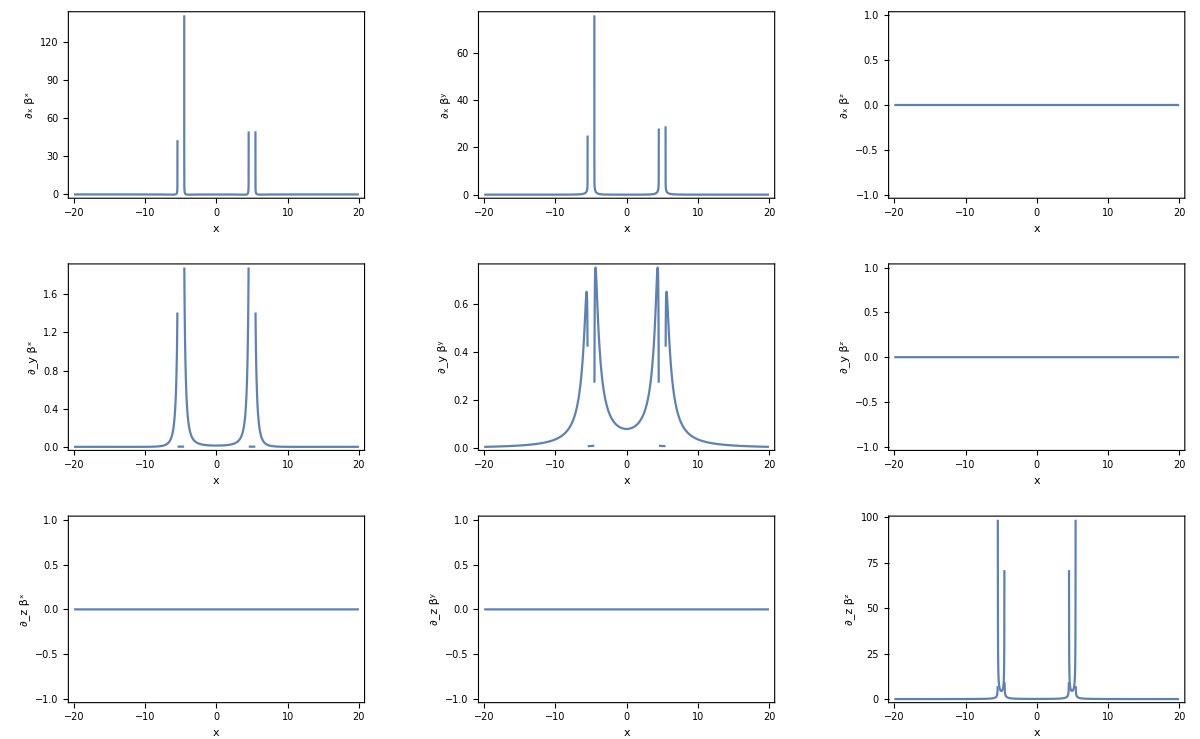

```mathematica
Block[
{expr1,expr2,expr3,expr4,expr5,expr6,expr7,expr8,expr9},

expr1=D[ushift⟦1⟧,x]//.{t->0,y->0,z->0};
expr2=D[ushift⟦2⟧,x]//.{t->0,y->0,z->0};
expr3=D[ushift⟦3⟧,x]//.{t->0,y->0,z->0};

expr4=D[ushift⟦1⟧,y]//.{t->0,y->0,z->0};
expr5=D[ushift⟦2⟧,y]//.{t->0,y->0,z->0};
expr6=D[ushift⟦3⟧,y]//.{t->0,y->0,z->0};

expr7=D[ushift⟦1⟧,z]//.{t->0,y->0,z->0};
expr8=D[ushift⟦2⟧,z]//.{t->0,y->0,z->0};
expr9=D[ushift⟦3⟧,z]//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_x β^x"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_x β^y"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr3,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_x β^z"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr4,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_y β^x"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr5,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_y β^y"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr6,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_y β^z"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr7,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_z β^x"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr8,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_z β^y"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr9,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x","∂_z β^z"},Axes->False,Frame->True,ImageSize->Large],
}
},
ImageSize->Full
]
]
```

### Chirs

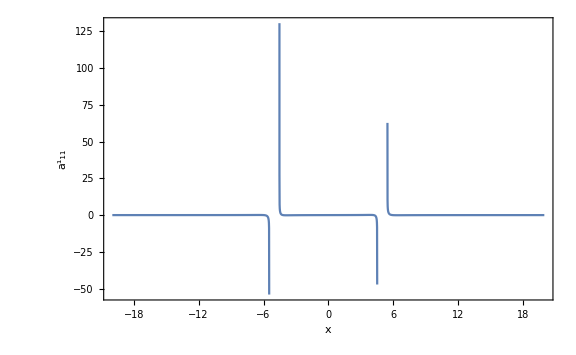

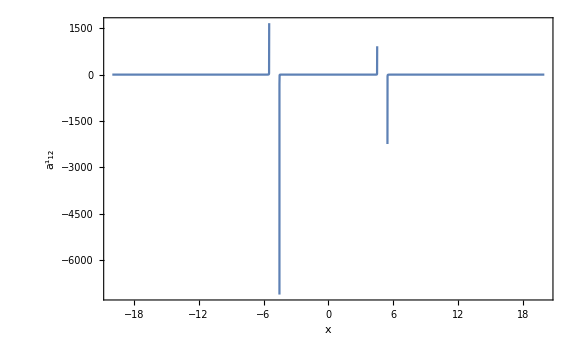

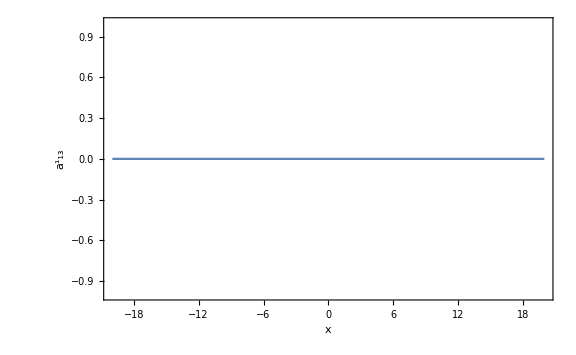

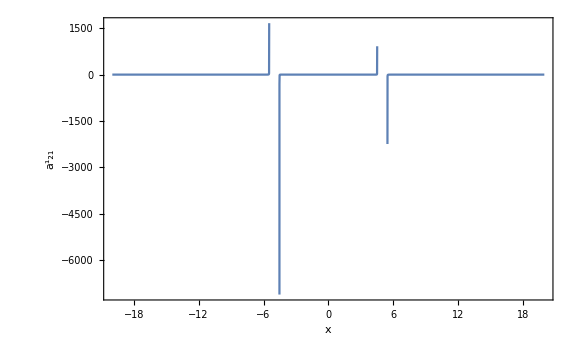

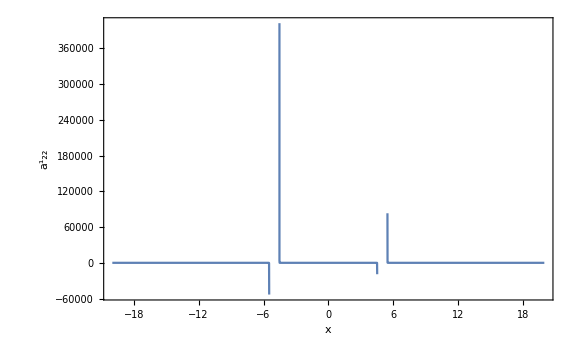

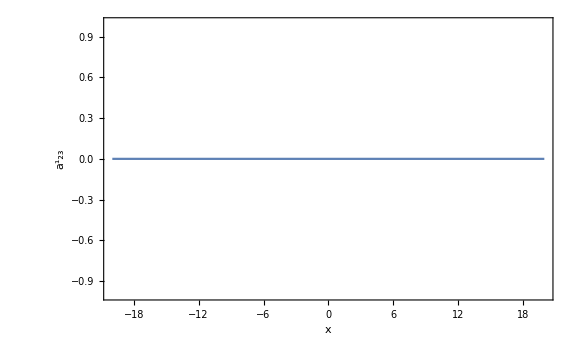

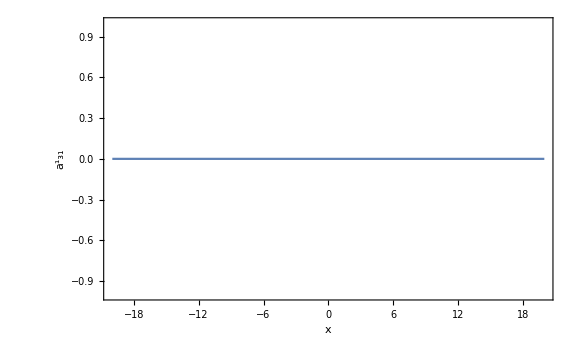

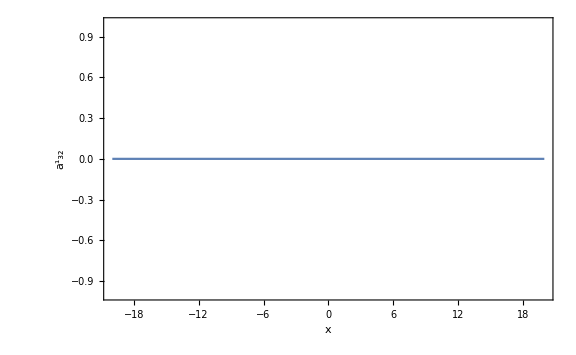

```mathematica
Block[
{expr},

Do[
expr=Γ⟦i,j,k⟧//.{t->0,y->0,z->0};

Plot[expr,{x,-20,20},PlotRange->{Full,Full},FrameLabel->{"x",Subscript[Superscript["a",ToString[i]],ToString[j]<>ToString[k]]},Axes->False,Frame->True,ImageSize->Large]//Print,

{i,1,3},{j,1,3},{k,1,3}
]
]
```

### lower extrinsic

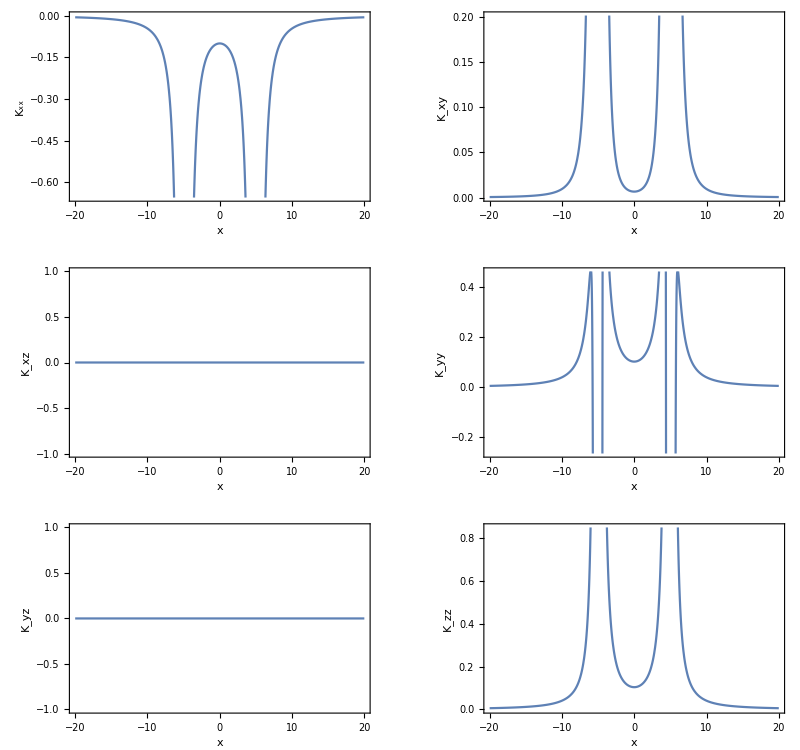

```mathematica
Block[
{expr1,expr2,expr3,expr4,expr5,expr6},

expr1=llextrinsic⟦1,1⟧//.{t->0,y->0,z->0};
expr2=llextrinsic⟦1,2⟧//.{t->0,y->0,z->0};
expr3=llextrinsic⟦1,3⟧//.{t->0,y->0,z->0};
expr4=llextrinsic⟦2,2⟧//.{t->0,y->0,z->0};
expr5=llextrinsic⟦2,3⟧//.{t->0,y->0,z->0};
expr6=llextrinsic⟦3,3⟧//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_xx"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_xy"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr3,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_xz"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr4,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_yy"},Axes->False,Frame->True,ImageSize->Large],
},
{
Plot[expr5,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_yz"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr6,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_zz"},Axes->False,Frame->True,ImageSize->Large],
}
},
ImageSize->Full
]
]
```

### ul extrinsic

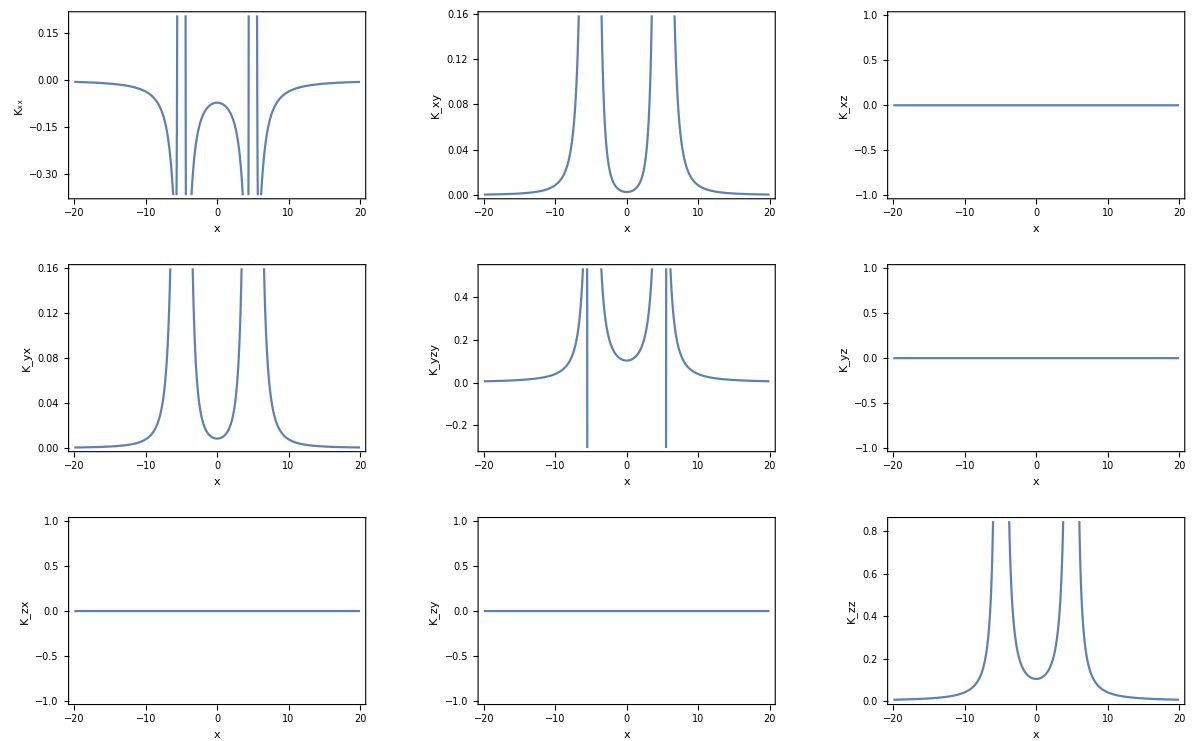

```mathematica
Block[
{expr1,expr2,expr3,expr4,expr5,expr6,expr7,expr8,expr9},

expr1=ulextrinsic⟦1,1⟧//.{t->0,y->0,z->0};
expr2=ulextrinsic⟦1,2⟧//.{t->0,y->0,z->0};
expr3=ulextrinsic⟦1,3⟧//.{t->0,y->0,z->0};
expr4=ulextrinsic⟦2,1⟧//.{t->0,y->0,z->0};
expr5=ulextrinsic⟦2,2⟧//.{t->0,y->0,z->0};
expr6=ulextrinsic⟦2,3⟧//.{t->0,y->0,z->0};
expr7=ulextrinsic⟦3,1⟧//.{t->0,y->0,z->0};
expr8=ulextrinsic⟦3,2⟧//.{t->0,y->0,z->0};
expr9=ulextrinsic⟦3,3⟧//.{t->0,y->0,z->0};

GraphicsGrid[
{
{
Plot[expr1,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_xx"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr2,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_xy"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr3,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_xz"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[expr4,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_yx"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr5,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_yzy"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr6,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_yz"},Axes->False,Frame->True,ImageSize->Large]
},
{
Plot[expr7,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_zx"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr8,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_zy"},Axes->False,Frame->True,ImageSize->Large],
Plot[expr9,{x,-20,20},PlotRange->{Full,Automatic},FrameLabel->{"x","K_zz"},Axes->False,Frame->True,ImageSize->Large]
}
},
ImageSize->Full
]
]
```